```mathematica
(* R0 = R00 for all alleles, IC50 = IC50 for all alleles.
Various plots of selection coefficient as a function of changing R00, IC50, and c of various alleles. Used for Jensen's Inequality section in thesis. *)
```

```mathematica
R0 = {1.398,1.275,1.227,0,1.37,1.375,1.397,1.219,1.119,1.184,1.306,1,1.273,1.282,1.45,1.250}
```

{1.398,1.275,1.227,0,1.37,1.375,1.397,1.219,1.119,1.184,1.306,1,1.273,1.282,1.45,1.25}

```mathematica
IC50 = {-6.286,-5.812,-4.239,0,-6.046,-5.774,-3.732,-3.55,-5.724,-5.491,-4.015,-4.6,-5.773,-5.624,-3.587,-3.3}
```

{-6.286,-5.812,-4.239,0,-6.046,-5.774,-3.732,-3.55,-5.724,-5.491,-4.015,-4.6,-5.773,-5.624,-3.587,-3.3}

```mathematica
(* Correct function, for some reason can't do multiple arguments in f*)
(* r0A,B = drugless growth rate
IC50A,B = IC50 (log concentration)
cA,B = scalar constant for slope of IC50 (always constant -0.685)
mu = Average drug concentration of step function 
width = determines the upper/lower bounds (mu + width = upper)
Function calculates selection coefficient of a step function in regards to the drug range specified by mu,width. *)
g[r0A_,r0B_,IC50A_,IC50B_,cA_,cB_,mu_,width_]:=
(-Exp[0.5*((r0A /(1+Exp[(IC50A - (mu + width))/cA])) +(r0A/(1+Exp[(IC50A-(mu-width))/cA])))] + Exp[0.5*((r0B /(1+Exp[(IC50B - (mu + width))/cB])) +(r0B/(1+Exp[(IC50B-(mu - width))/cB])))])/(Exp[0.5*((r0A /(1+Exp[(IC50A - (mu + width))/cA])) +(r0A/(1+Exp[(IC50A-(mu - width))/cA])))])
```

```mathematica
g[r0A_,r0B_,IC50A_,IC50B_,cA_,cB_,mu_,width_]
```

ⅇ^(-0.5 (r0A_/(1+ⅇ^((IC50A_-mu_-width_)/cA_))+r0A_/(1+ⅇ^((IC50A_-mu_+width_)/cA_)))) (-ⅇ^(0.5 (r0A_/(1+ⅇ^((IC50A_-mu_-width_)/cA_))+r0A_/(1+ⅇ^((IC50A_-mu_+width_)/cA_))))+ⅇ^(0.5 (r0B_/(1+ⅇ^((IC50B_-mu_-width_)/cB_))+r0B_/(1+ⅇ^((IC50B_-mu_+width_)/cB_)))))

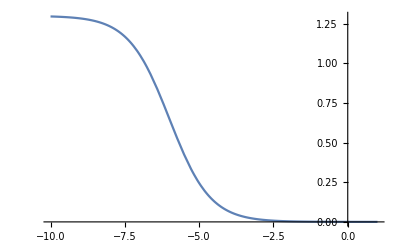

```mathematica
(* g[r0_,IC50_,c_, 
Find a function to plot the actual growth curve
*)
h[r0_,IC50_,c_,x_]:= r0/(1+Exp[(IC50 - (x))/c])
Plot[h[1.3,-6,-0.685,x],{x,1,-10}]
```

```mathematica
(* Solve[{g[1,1.2,-6,-6.4,-0.685,-0.685,a,b]==0,a>0 , b>0},{a},Reals] *)
```

Dan playing here to illustrate some ideas

```mathematica
a:=1.2;
NSolve[{g[a,b,-6,-6.5,-0.685,-0.685,-6,2]==0 , b>0},{b},Reals]
```

{{b→1.29776}}

```mathematica
a:=List[1,1.1,1.2,1.3,1.4,1.5];
NSolve[{g[a,b,-6,-6.5,-0.685,-0.685,-6,2]==0 , b>0},{b},Reals]
```

{}

```mathematica
(* NSolve[{g[a,b,-6,-6,-0.685,-0.685,-6,2]==0 , a>0 , b>0},{a,b},Reals] *)
```

```mathematica
(* R0A = R0B, IC50A = IC50B -> equal selection coefficient*)
 Plot3D[g[1,1,-6,-6,-0.685,-0.685,a,b],{a,-3,-7},{b,0,2}]
```

-Graphics3D-

-Graphics3D-

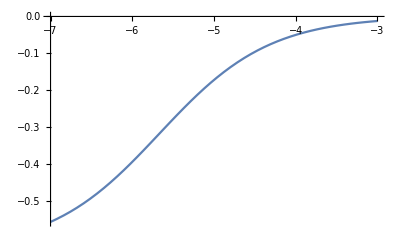

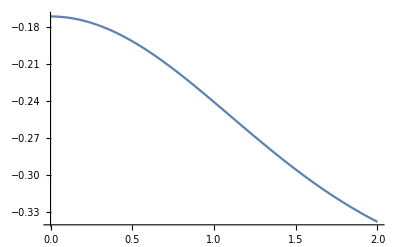

```mathematica
(* R0A > R0B, IC50A = IC50B -> selection coefficient always negative *)
Plot3D[{g[2,1,-6,-6,-0.685,-0.685,a,b],0},{a,-3,-7},{b,0,2}]
Plot[g[2,1,-6,-6,-0.685,-0.685,a,0],{a,-3,-7}]
Plot[g[2,1,-6,-6,-0.685,-0.685,-5,b],{b,0,2}]
```

```mathematica
(* R0A > R0B, IC50A > IC50B -> Selection coefficient always negative *)
 Plot3D[{g[1.2,1,-6,-6.1,-0.685,-0.685,a,b],0},{a,-3,-7},{b,0,2}]
```

-Graphics3D-

```mathematica
(* R0A = R0B, IC50A > IC50B -> Selection coefficient always negative *)
 Plot3D[{g[1,1,-6,-6.2,-0.685,-0.685,a,b],0},{a,-1,-7},{b,0,2}]
```

-Graphics3D-

-Graphics3D-

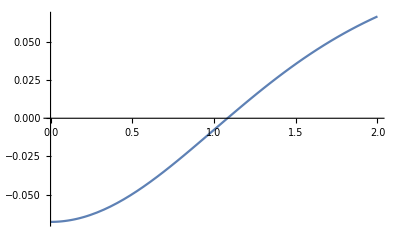

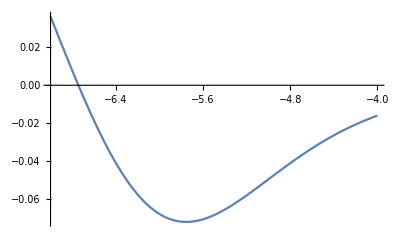

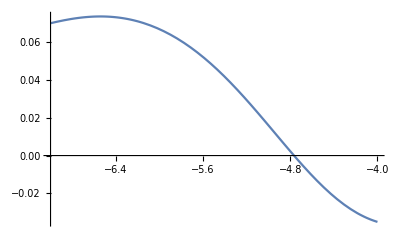

```mathematica
(* R0A < R0B, IC50A > IC50B*) Plot3D[{g[1,1.2,-6,-6.4,-0.685,-0.685,a,b],0},{a,-3,-7},{b,0,2}]
Plot[g[1,1.2,-6,-6.4,-0.685,-0.685,-6,b],{b,0,2}] (* variance *)
Plot[g[1,1.2,-6,-6.4,-0.685,-0.685,b,0],{b,-4,-7}] (* mean *)
Plot[g[1,1.2,-6,-6.4,-0.685,-0.685,b,2],{b,-4,-7}] (* mean with greater variance *)
```

```mathematica
(* Varying R0A and R0B, keeping IC50A,B and mu,width constant *)
Plot3D[{g[a,b,-6,-6.4,-0.685,-0.685,-6,2],0},{a,1,5},{b,1,5}]
```

-Graphics3D-

```mathematica
(* Varying IC50A and IC50B, keeping R0A,B and mu,width constant *)
 Plot3D[{g[1,1.2,a,b,-0.685,-0.685,-6,2],0},{a,-3,-8},{b,-3,-8}]
```

-Graphics3D-

```mathematica
(* With enough variance, can incur a sign switch in selection coefficient *)
Plot3D[{g[1.5,1.2,-6,-5,-0.685,-0.685,a,b],0},{a,0,-10},{b,0,5}]
```

-Graphics3D-

```mathematica
(* Observing how increasing difference in IC50 moves the transition mu,width for sign switch of selection coefficient, and also when switch is most prominent *)
Plot3D[{g[1,1.2,-6,-6.6,-0.685,-0.685,a,b],g[1,1.2,-6,-6.5,-0.685,-0.685,a,b],g[1,1.2,-6,-6.4,-0.685,-0.685,a,b],g[1,1.2,-6,-6.3,-0.685,-0.685,a,b],0},{a,-4,-7},{b,0,2}]
```

-Graphics3D-

```mathematica
p1 = Plot3D[{g[1,1.2,-6,-6.6,-0.685,-0.685,a,b],0},{a,-4,-7},{b,0,2}]
p2 = Plot3D[{g[1,1.2,-6,-6.5,-0.685,-0.685,a,b],0},{a,-4,-7},{b,0,2}]
p3 =Plot3D[{g[1,1.2,-6,-6.4,-0.685,-0.685,a,b],0},{a,-4,-7},{b,0,2}]
p4 = Plot3D[{g[1,1.2,-6,-6.3,-0.685,-0.685,a,b],0},{a,-4,-7},{b,0,2}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
Plot3D[{g[1,1.2,-3,-3.4,-0.685,-0.685,a,b],0},{a,-2,-7},{b,0,2}]
```

-Graphics3D-

```mathematica
Plot3D[{g[2,2.4,-8,-8.6,-0.685,-0.685,a,b],0},{a,-5,-10},{b,0,2}]
```

-Graphics3D-

```mathematica
Plot3D[{g[2,2.4,-8,-8.6,-0.685,-0.685,a,b],0},{a,-5,-10},{b,0,2}]
```

-Graphics3D-

-Graphics3D-

-0.0601913

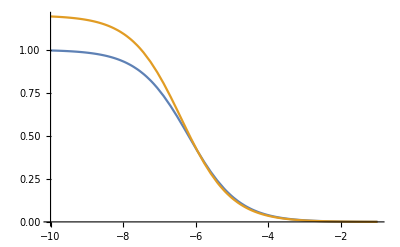

```mathematica
(* Early intuitions: if IC50s are similar and/or around the mean, then R0s must also be relatively close to engage in sign switch*) 
Plot3D[{g[a,b,-6.2,-6.4,-0.685,-0.685,-6,0.5],0},{a,1,12},{b,1,10},PlotRange->{-0.1,0.1}]
g[1,1,-6.2,-6.4,-0.685,-0.685,-6,0.5]
Plot[{h[1,-6.2,-0.685,x],h[1.2,-6.4,-0.685,x]},{x,-1,-10}]
```

-Graphics3D-

0.0186106

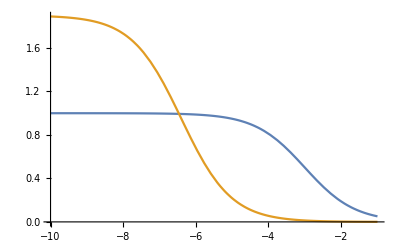

```mathematica
(* Not similar IC50, but one of the IC50s is near Mu.
When IC50s are not similar, but the higher R0, lower IC50 allele is around the mean, then requires a large R0 (1 vs. 1.9) to obtain sign change. Realistic: high R0 usually low IC50  *)
Plot3D[{g[a,b,-3,-6.4,-0.685,-0.685,-6.5,0.5],0},{a,1,12},{b,1,10}]
g[1,1.9,-3,-6.4,-0.685,-0.685,-6.5,0.5]
Plot[{h[1,-3,-0.685,x],h[1.9,-6.4,-0.685,x]},{x,-1,-10}]
```

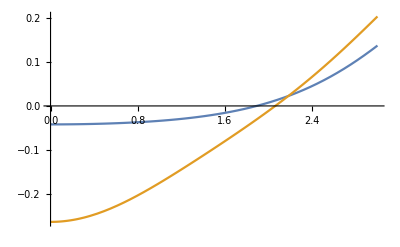

```mathematica
Plot[{g[1,1.9,-3,-6.4,-0.685,-0.685,-6.4,w],g[1,1.9,-3,-6.4,-0.685,-0.685,-6,w]},{w,0,3}]
```

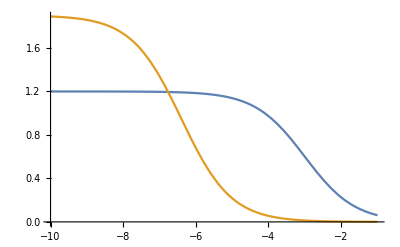

```mathematica
Plot[{h[1.2,-3,-0.685,x],h[1.9,-6.4,-0.685,x]},{x,-1,-10}]
```

-Graphics3D-

0.0872197

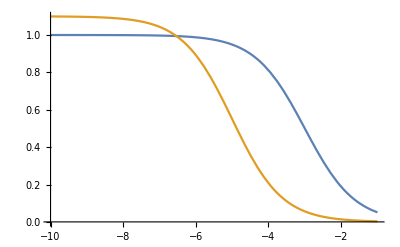

```mathematica
(* Not similar IC50s, and also mu is not close to either IC50 (mu is much lower).
If mu (including variance) is not close to either IC50. Then R0 plays a big role in selection coefficient (controls the height) *)
Plot3D[{g[a,b,-3,-5,-0.685,-0.685,-8,0.5],0},{a,1,12},{b,1,10}]
g[1,1.1,-3,-5,-0.685,-0.685,-8,0.5]
Plot[{h[1,-3,-0.685,x],h[1.1,-5,-0.685,x]},{x,-1,-10}]
```

-Graphics3D-

0.0194805

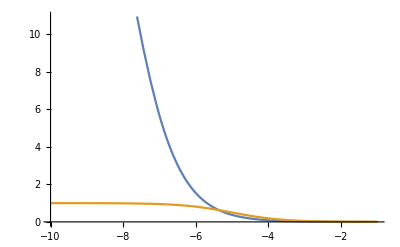

```mathematica
(* IC50s are not similar, and mu is located much higher than both IC50s, no plausible R0 can invoke a sign change. Sign change is much more dependent on IC50s relationship to mu. *)
Plot3D[{g[a,b,-8,-5,-0.685,-0.685,-2.5,0.5],0},{a,1,12},{b,1,10}]
g[30,1,-8,-5,-0.685,-0.685,-2.5,0.5]
Plot[{h[30,-8,-0.685,x],h[1,-5,-0.685,x]},{x,-1,-10}]
```

-Graphics3D-

0.0979609

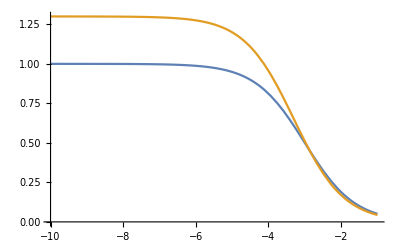

```mathematica
(* Similar IC50s but not near mu. Mu is much smaller than IC50 concentration, pretty much entirely dependent on R0.
Easy to change sign, very sensitive to R0.  *)
Plot3D[{g[a,b,-3,-3.3,-0.685,-0.685,-6.5,0.5],0},{a,1,12},{b,1,10}]
g[1.3,1.4,-3,-3.3,-0.685,-0.685,-6.5,0.5]
Plot[{h[1,-3,-0.685,x],h[1.3,-3.3,-0.685,x]},{x,-1,-10}]
```

-Graphics3D-

-0.0081221

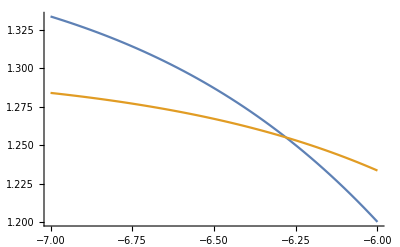

```mathematica
(* Realistic R0s, R0A > R0B, IC50A < IC50B
Difference in IC50 is not large with realistic R0 
Increasing variance favors allele B. *)
Plot3D[{g[1.38,1.3,a,b,-0.685,-0.685,-6.5,0.5],0},{a,-1,-12},{b,-1,-10}]
g[1.38,1.3,-4.7,-4,-0.685,-0.685,-6.5,0.5]
Plot[{h[1.38,-4.7,-0.685,x],h[1.3,-4,-0.685,x]},{x,-6,-7}]
```

-Graphics3D-

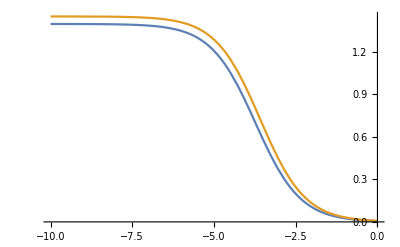

```mathematica
(* Real plot of Allele A (0110 (6)), Allele B (1110 (14))
The 2nd highest ranked allele can never beat the highest ranked allele because R0 and IC50 are both higher *)
Plot3D[{g[1.397,1.45,-3.732,-3.587,-0.685,-0.685,a,b],0},{a,0,-10},{b,0,10}]
Plot[{h[1.397,-3.732,-0.685,x],h[1.45,-3.587,-0.685,x]},{x,0,-10}]
```

-Graphics3D-

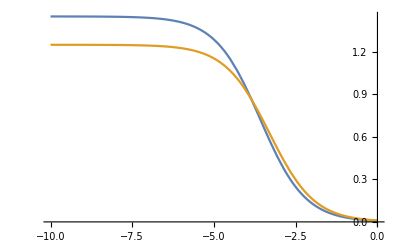

```mathematica
(* Allele 14 (1110) to Allele 15 (1111) fully evolved allele
What parameters does it take to reach quadruple mutant *)
Plot3D[{g[1.45,1.25,-3.587,-3.3,-0.685,-0.685,a,b],0},{a,0,-10},{b,0,10}]
Plot[{h[1.45,-3.587,-0.685,x],h[1.25,-3.3,-0.685,x]},{x,0,-10}]
```

-Graphics3D-

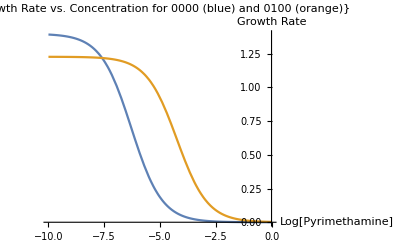

```mathematica
Plot3D[{g[R0[[1]],R0[[3]],IC50[[1]],IC50[[3]],-0.685,-0.685,a,b],0},{a,0,-10},{b,0,10},PlotLabel->{"Selection Coefficient for 0000 (blue) and 0100 (orange)"},AxesLabel->{"Average Drug Concentration","Step Size (Variance)","Selection Coefficient"}]
Plot[{h[R0[[1]],IC50[[1]],-0.685,x],h[R0[[3]],IC50[[3]],-0.685,x]},{x,0,-10},PlotLabel->{"Growth Rate vs. Concentration for 0000 (blue) and 0100 (orange)"},AxesLabel->{"Log[Pyrimethamine]","Growth Rate"}]
```

```mathematica
Show[%213,ImageSize->Large]
```

-Graphics3D-

```mathematica
Plot3D[{g[R0[[1]],R0[[6]],IC50[[1]],IC50[[6]],-0.685,-0.685,a,b],0},{a,0,-10},{b,0,10}]
```

-Graphics3D-

```mathematica
Plot3D[{g[R0[[1]],R0[[10]],IC50[[1]],IC50[[10]],-0.685,-0.685,a,b],0},{a,0,-10},{b,0,10}]
```

-Graphics3D-

```mathematica
Plot3D[{g[R0[[5]],R0[[13]],IC50[[5]],IC50[[13]],-0.685,-0.685,a,b],0},{a,0,-10},{b,0,10}]
```

-Graphics3D-

```mathematica
Plot3D[{g[R0[[5]],R0[[7]],IC50[[5]],IC50[[7]],-0.685,-0.685,a,b],0},{a,0,-10},{b,0,10}]
```

-Graphics3D-

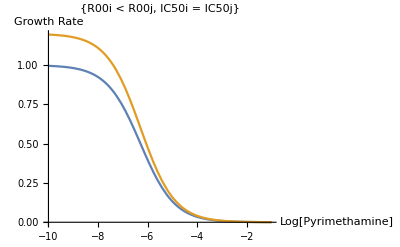

```mathematica
Plot[{h[1,IC50[[1]],-0.685,x],h[1.2,IC50[[1]],-0.685,x]},{x,-1,-10},AxesLabel->{"Log[Pyrimethamine]","Growth Rate"},PlotLabel->{"R00i < R00j, IC50i = IC50j"}]
```

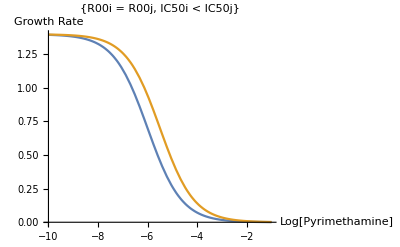

```mathematica
Plot[{h[R0[[1]],-6,-0.685,x],h[R0[[1]],-5.5,-0.685,x]},{x,-1,-10},AxesLabel->{"Log[Pyrimethamine]","Growth Rate"},PlotLabel->{"R00i = R00j, IC50i < IC50j"}]
```

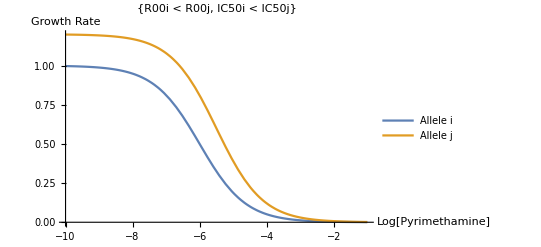

```mathematica
Plot[{h[1,-6,-0.685,x],h[1.2,-5.5,-0.685,x]},{x,-1,-10},AxesLabel->{"Log[Pyrimethamine]","Growth Rate"},PlotLabel->{"R00i < R00j, IC50i < IC50j"},PlotLegends->{"Allele i","Allele j"}]
```

```mathematica
Plot3D[{g[R0[[1]],R0[[3]],IC50[[1]],IC50[[3]],-0.685,-0.685,a,b],0},{a,0,-10},{b,0,10},AxesLabel->{"μ (Concentration \n in log(M))","ω (0.5*Step Size \n in log(M))","s i->j"}]
```

-Graphics3D-

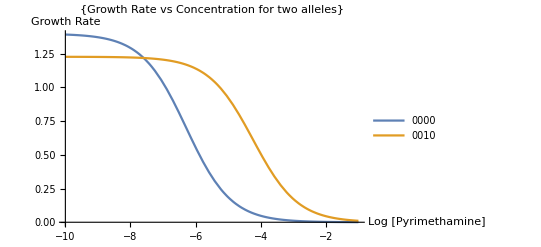

```mathematica
Plot[{h[R0[[1]],IC50[[1]],-0.685,x],h[R0[[3]],IC50[[3]],-0.685,x]},{x,-1,-10},AxesLabel->{"Log\n[Pyrimethamine]","Growth \nRate"},PlotLabel->{"Growth Rate vs Concentration \nfor two alleles"},PlotLegends->{"0000","0010"},LabelStyle->{(FontSize->13)}]
```

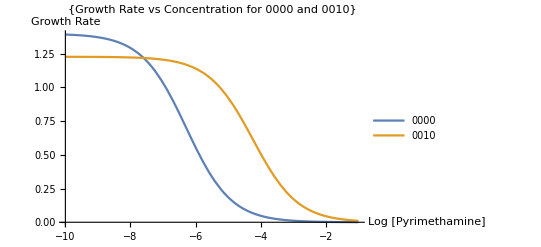

-Graphics-

```mathematica
(* Below is a simplified contour plot showing which regions are positive or negative given the certain conditions. *)
```

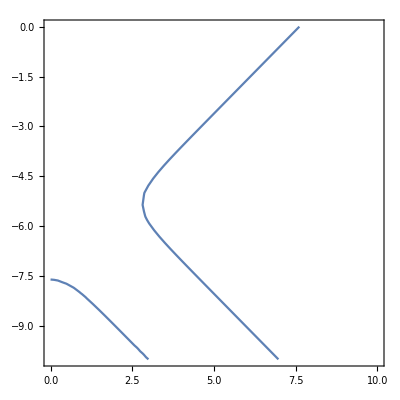

```mathematica
ContourPlot[g[R0[[1]],R0[[3]],IC50[[1]],IC50[[3]],-0.685,-0.685,a,b]==0,{b,0,10},{a,0,-10}]
```

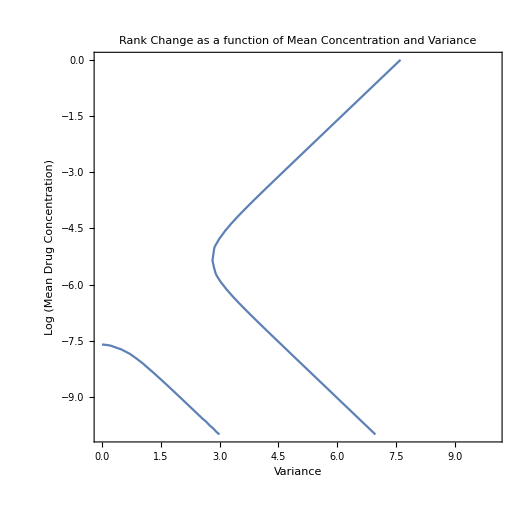

```mathematica
Show[%258,FrameLabel->{{HoldForm[Log (Mean Drug Concentration)],None},{HoldForm[Variance],None}},PlotLabel->HoldForm[Rank Change as a function of Mean Concentration and Variance],LabelStyle->{13,GrayLevel[0],Bold}]
```

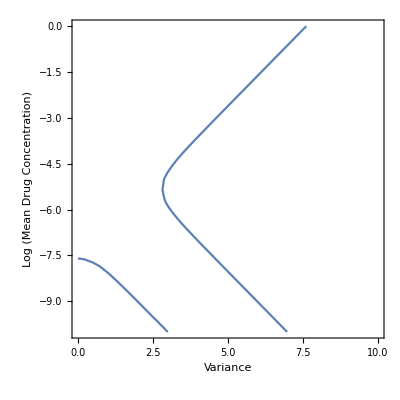

```mathematica
Show[%259,PlotLabel->None,LabelStyle->{FontFamily->"Calibri",24,GrayLevel[0]}]
```